```mathematica
(*Replace your Lean executable here.
If you have a standard installation with Lean in the system path,
  you can just use LeanExecutable = "lean". *)
```

```mathematica
LeanExecutable=FileNameJoin[{$HomeDirectory,".elan/bin/lean"}]
```

C:\Users\jackh\.elan\bin\lean

```mathematica
(*Set the working directory to be mm_lean/src/ 
If you opened this file from that directory, this may already be set.
Check this by evaluating Directory[] *)
```

```mathematica
Directory[]
```

C:\Users\jackh\OneDrive\Documents

```mathematica
SetDirectory["C:\\Public\\WSS2023\\mm-lean\\src"]
```

C:\Public\WSS2023\mm-lean\src

```mathematica
<<"main.m";
```

```mathematica
Lean=LeanMode[]
```

```mathematica
ProcessObject[…]
```

ProcessObject[…]

```mathematica
ProcessStatus[Lean]
```

Running

```mathematica
leanProof = GetLeanProof[Lean,"nat.prime.dvd_of_dvd_pow"]
```

Goal | ∀ {p m n : ℕ}, nat.prime p → p ∣ m ^ n → p ∣ m
ID | 24
Rule | ∀I
Proofs |

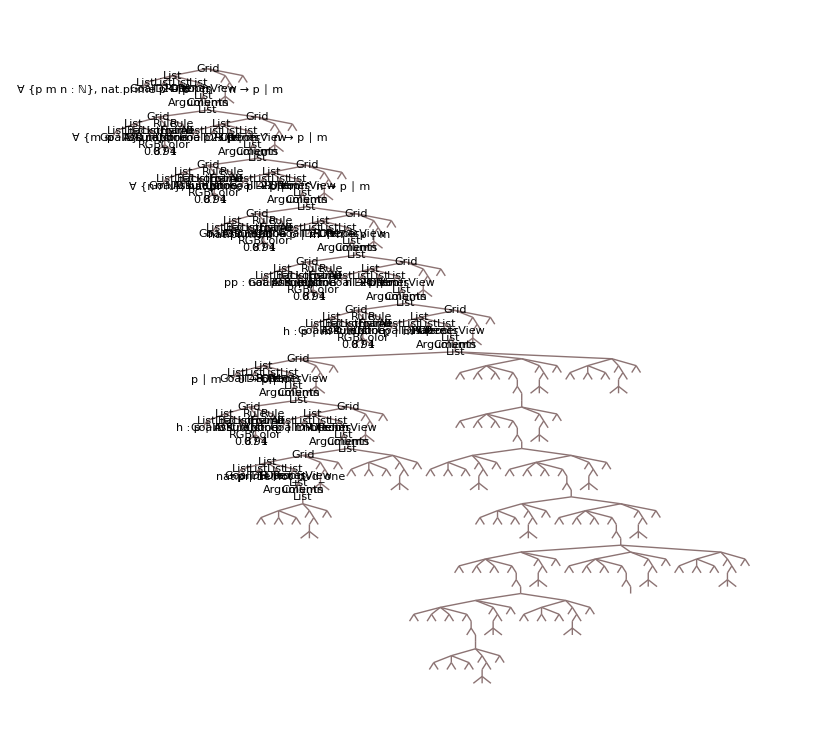

```mathematica
leanProof // TreeForm
```

```mathematica
leanProofCases = Cases[leanProof, List[ID,_], Infinity];
```

```mathematica
leanProofPositions = Position[leanProof, List[ID,_], Infinity];
```

```mathematica
leanProofMap = MapThread[{#1[[2]],Length[#2]}&,{leanProofCases,leanProofPositions}] ;
```

```mathematica
leanProofMapSorted = SortBy[leanProofMap, Last] (* not strictly *)
```

{{24,2},{0,9},{23,9},{1,16},{22,16},{2,23},{21,23},{3,30},{20,30},{4,37},{19,37},{4,44},{8,44},{18,44},{5,51},{7,51},{17,51},{5,58},{6,58},{10,58},{16,58},{3,65},{11,65},{15,65},{10,72},{13,72},{14,72},{11,79},{12,79},{3,86}}

```mathematica
MapIndexed[{#1[[1]],#2[[1]]}&,leanProofMapSorted]
```

{{24,1},{0,2},{23,3},{1,4},{22,5},{2,6},{21,7},{3,8},{20,9},{4,10},{19,11},{4,12},{8,13},{18,14},{5,15},{7,16},{17,17},{5,18},{6,19},{10,20},{16,21},{3,22},{11,23},{15,24},{10,25},{13,26},{14,27},{11,28},{12,29},{3,30}}

```mathematica
Tree
```

```mathematica
GetLeanProof[Lean,"nat.prime.dvd_of_dvd_pow"]// Extract[{1,2,2}]
```

24

```mathematica
GetLeanProof[Lean,"nat.prime.not_coprime_iff_dvd"]
```

Goal | ∀ {m n : ℕ}, ¬m.coprime n ↔ ∃ (p : ℕ), nat.prime p ∧ p ∣ m ∧ p ∣ n
ID | 28
Rule | ∀I
Proofs |

```mathematica
GetLeanProof[Lean,"nat.exists_infinite_primes"]
```

Goal | ∀ (n : ℕ), ∃ (p : ℕ), n ≤ p ∧ nat.prime p
ID | 31
Rule | ∀I
Proofs |

```mathematica
GetLeanInfo[Lean, "nat.min_fac"]
```

Category | Definition
Type | ℕ → ℕ
Description |

```mathematica
GetLeanInfo[Lean, "nat.exists_infinite_primes"]
```

Category | Theorem
Type | ∀ (n : ℕ), ∃ (p : ℕ), n ≤ p ∧ nat.prime p
Description |

```mathematica
GetLeanProof[Lean,"Set.singleton_inj"]
```

Goal | ∀ {x y : Set}, {x} = {y} → x = y
ID | 14
Rule | ∀I
Proofs |

```mathematica
GetLeanProof[Lean,"Set.regularity"]
```

Goal | ∀ (x : Set), x ≠ ∅ → (∃ (y : Set) (H : y ∈ x), x ∩ y = ∅)
ID | 42
Rule | ∀I
Proofs |

```mathematica
ProveUsingLeanTactic[Lean,ForAllTyped[{p,q,r},Prop,Implies[Implies[p,Implies[q,r]],Implies[And[p,q],r]]],"mm_prover", True]
```

Goal | ∀ (p q r : Prop), (p → q → r) → p ∧ q → r
ID | 12
Rule | ∀I
Proofs |

```mathematica
RunLeanTactic[Lean,ForAllTyped[{p,q,r},Prop,Implies[Implies[p,Implies[q,r]],Implies[And[p,q],r]]],"print_translation",True]
```

Lean native | ∀ (p q r : Prop), (p → q → r) → p ∧ q → r
Mathematica form |

```mathematica
<<"../_target/deps/mathematica/src/lean_form.m"
```

```mathematica
<<"natural_deduction_graphs.wl"
```

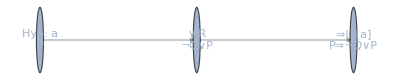

```mathematica
DiagramOfFormula[Lean,ForAll[{P,Q},Implies[P,Or[Not[Q],P]]],{P,Q}]
```

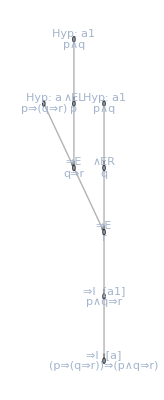

```mathematica
DiagramOfFormula[Lean,ForAllTyped[{p,q,r},Prop,Implies[Implies[p,Implies[q,r]],Implies[And[p,q],r]]],{p,q,r}]
```

```mathematica
RunLeanTactic[Lean,ForAllTyped[{s,t},set[nat],SetInter[s,SetUnion[t,SetCompl[s]]]==SetInter[s,t]],"normalize_set_lemmas"]
```

set_distrib_right : ∀ {α : Type ?} (s t u : set α), s ∩ (t ∪ u) = s ∩ t ∪ s ∩ u
set.union_empty : ∀ {α : Type ?} (a : set α), a ∪ ∅ = a
set.inter_compl_self : ∀ {α : Type ?} (s : set α), s ∩ sᶜ = ∅

```mathematica
ProveUsingLeanTactic[Lean,ForAllTyped[{s,t},set[nat],SetInter[s,SetUnion[t,SetCompl[s]]]==SetInter[s,t]],"simp", True]
```

Goal | ∀ (s t : set ℕ), s ∩ (t ∪ sᶜ) = s ∩ t
ID | 56
Rule | eq.mpr
Proofs |

```mathematica
SelectLeanPremises[Lean,ForAllTyped[{x,y},real,Implies[x<y,Exists[{z},And[x<z, z<y]]]]]
```

```mathematica
QuitLeanMode[Lean]
```